```mathematica
m:=10
l:=Sqrt[1]
n:=5
d:=3
"causal events" n
"causal relations" n^2
A=CSMinkowski3Diamond[l,n];
ρ:=CSize[A] / CVolume[A]
"density" ρ
Subscript[C, 1]=CausalMatrix[A];

V=(IdentityMatrix[n]+Subscript[C, 1]).(IdentityMatrix[n]+Subscript[C, 1]);
Subscript[T, 2]=Sqrt[2/ρ]*Sqrt[V];  
K=1/2 Subscript[C, 1].Inverse[IdentityMatrix[n]+m^2/(2ρ)Subscript[C, 1]];

Z:=Im[Table[Sqrt[(A[[1,i,1]]-A[[1,j,1]])^2+(A[[1,i,2]]-A[[1,j,2]])^2-(A[[1,i,3]]-A[[1,j,3]])^2],{i,n},{j,n}]];
Time=Subscript[C, 1]*Z;

points:=Transpose[{Flatten[Time],Flatten[K]}];

A //MatrixForm
```

5 causal events

25 causal relations

19.0986 density

({{-0.0995905,-0.135504,-0.237739},{0.0606325,-0.32386,-0.134095},{0.201282,0.0991689,-0.0796688},{0.00439267,-0.205156,0.00529916},{0.0587496,-0.116131,0.104044}}
CSMinkowski3Diamond
3
5
0.261799
1)

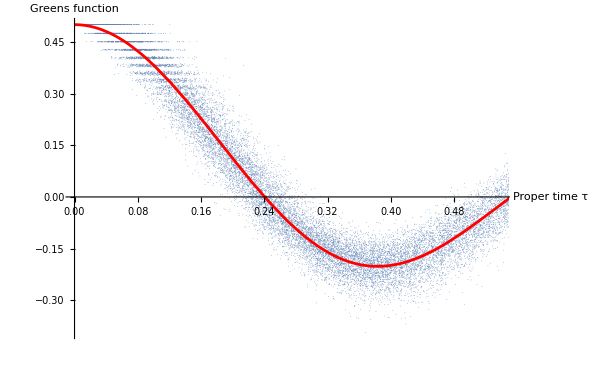

```mathematica
sample:=100000
(*ListPlot[RandomSample[points,sample],PlotStyle->PointSize[0.00001],ImageSize->600,AxesLabel->{"Matrix 1 entries","Matrix 2 entries"}]
Plot[1/2 BesselJ[0,m*x],{x,0,l}]
*)
Subscript[plot, 1]=ListPlot[RandomSample[points,sample],PlotStyle->PointSize[0.00001],ImageSize->600,AxesLabel->{"Proper time τ","Greens function"}];
Subscript[plot, 2]=Plot[1/2 BesselJ[0,m*x],{x,0,l},PlotStyle->Red];
Show[Subscript[plot, 1],Subscript[plot, 2]]
```

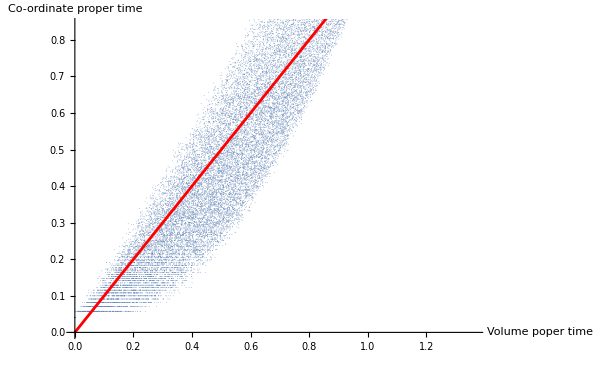

```mathematica
sample:=100000
times=Transpose[{Flatten[T],Flatten[Subscript[T, 2]]}];
Subscript[plot, 3]=ListPlot[RandomSample[times,sample],PlotStyle->PointSize[0.00001],ImageSize->600,AxesLabel->{"Volume poper time","Co-ordinate proper time"}];
Subscript[plot, 4]=Plot[x,{x,0,l},PlotStyle->Red];
Show[Subscript[plot, 3],Subscript[plot, 4]]
```